# gaussian smearing

## δ switch, g smear, go futher with the transition probability

## the smearing function

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1}]
```

#### simplify the fourier transform

```mathematica
ftil[k]
```

(ⅇ^(-1/4 k^2 σ^2))/(√(1/σ^2) σ)

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftilGs[k_]:=ⅇ^(-1/4 k^2 σ^2)
```

## the transition probability

```mathematica
ggintegrandG[k_]:=(1-2*α)/(2π)*ⅇ^(-ε*k)*k*ftilGs[k]^2
```

#### with an ε regularized cutoff (exp)

```mathematica
Integrate[ggintegrandG[k],{k,0,∞}]
```

ConditionalExpression[-((-1+2 α) (2 σ^2-ⅇ^(ε^2/(2 σ^2)) √(2 π) ε √(σ^2)+ⅇ^(ε^2/(2 σ^2)) √(2 π) ε σ Erf[ε/(√2 σ)]))/(4 π σ^4),Re[σ^2]>0]

```mathematica
Simplify[Out[13],Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

```mathematica
pertexp[σ_]:=-((-1+2 α) (-ⅇ^(ε^2/(2 σ^2)) √(2 π) ε+2 σ+ⅇ^(ε^2/(2 σ^2)) √(2 π) ε Erf[ε/(√2 σ)]))/(4 π σ^3)
```

```mathematica
pexp[σ_]:=α+λ^2*pertexp[σ]
```

#### with no cutoff (ε:=0)

```mathematica
Simplify[pertexp[σ],Assumptions->ε==0]
```

```mathematica
pertnone[σ_]:=(1-2 α)/(2 π σ^2)
```

```mathematica
pnone[σ_]:=α+λ^2*pertnone[σ]
```

#### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
Integrate[ggintegrandG[k],{k,0,5*Ω}]
```

-1/(4 π σ^3)ⅇ^(-5/2 Ω (2 ε+5 σ^2 Ω)) (-1+2 α) (2 (-1+ⅇ^(5/2 Ω (2 ε+5 σ^2 Ω))) σ+ⅇ^(((ε+5 σ^2 Ω)^2)/(2 σ^2)) √(2 π) ε (Erf[ε/(√2 σ)]-Erf[(ε+5 σ^2 Ω)/(√2 σ)]))

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals]
```

```mathematica
pertsharp[σ_]:=-(ⅇ^(-25/2 σ^2 Ω^2) (-1+ⅇ^((25 σ^2 Ω^2)/2)) (-1+2 α))/(2 π σ^2)
```

```mathematica
psharp[σ_]:=α+λ^2*pertsharp[σ]
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v σ

#### assign the parameters numbers

```mathematica
Ω:=1
α:=0
λ:=0.1
```

```mathematica
ε:=.25
```

#### clear the parameters of their numbers when necessary

```mathematica
Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v σ

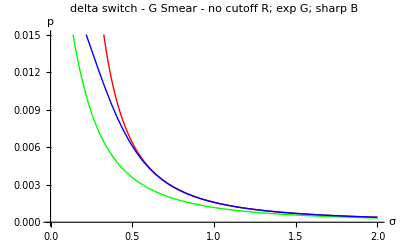

```mathematica
Plot[{pnone[σ],pexp[σ],psharp[σ]},{σ,0.1,2},
AxesLabel->{σ,p},
PlotRange->Automatic,
PlotStyle->{Red,Green,Blue},
PlotLabel->Style["delta switch - G Smear -\n no cutoff R; exp G; sharp B",FontSize->16]]
```

## status

i think we had expected that p would diverge for δ - δ. if that is the case it makes sense for p to diverge in the σ→0 limit for no cutoff. also indicates that a sharp cutoff has a larger effect on the effective size in the δ switching case than in the G switching case.